## Base Model (No Treatment options)

```mathematica
base={
S'[t]==-(β c S[t]U[t])/1000-(ω c S[t]P[t])/1000,
U'[t]==(β c S[t]U[t])/1000+(ω c S[t]P[t])/1000-α U[t],
P'[t]==ϵ α U[t]-μ P[t] ,
A'[t]==(1-ϵ)α U[t]+μ P[t],
S[0]==760,U[0]==200,P[0]==30,A[0]==10
	};
```

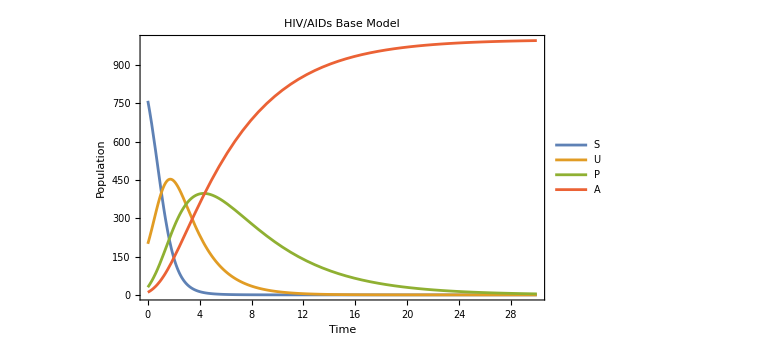

S[t]: {0.01772,760.}

U[t]: {0.0010883,446.44}

P[t]: {3.98155,395.48}

A[t]: {10.,996.}

```mathematica
params={α->0.5,β->.15,ω->0.2,ϵ->.784,μ->.2,c->10};
sol=NDSolve[base/.params,{S,U,P,A},{t,0,10000}];
Plot[Evaluate[{S[t],U[t],P[t],A[t]}/.sol],{t,0,30},
		PlotLabel->"HIV/AIDs Base Model",PlotLegends->Placed[{"S","U","P","A"},Right],Frame->True,Axes->False,FrameLabel->{"Time","Population"},
ImageSize->Large]

Print["S[t]: ",MinMax[Table[{S[t]}/. sol,{t,0,30}]]]
Print["U[t]: ",MinMax[Table[{U[t]}/. sol,{t,0,30}]]]
Print["P[t]: ",MinMax[Table[{P[t]}/. sol,{t,0,30}]]]
Print["A[t]: ",MinMax[Table[{A[t]}/. sol,{t,0,30}]]]
```

## Treatment 1 Model (Testing & Education)

```mathematica
treat1={
S'[t]==-(β c S[t]U[t])/1000-(ω c S[t]P[t])/1000-τ S[t],
U'[t]==(β c S[t]U[t])/1000+(ω c S[t]P[t])/1000-α U[t]+τ S[t],
P'[t]==ϵ α U[t]-μ P[t] ,
A'[t]==(1-ϵ)α U[t]+μ P[t],
S[0]==760,U[0]==200,P[0]==30,A[0]==10
	};
```

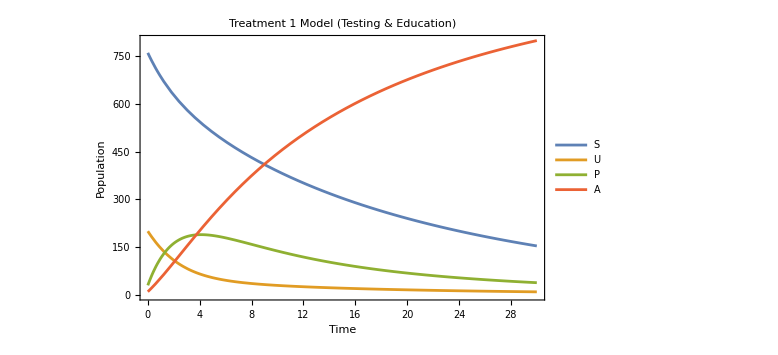

S[t]: {153.69,760.}

U[t]: {9.54242,200.}

P[t]: {30.,189.1}

A[t]: {10.,798.492}

```mathematica
params1={α->0.75,β->(.15)/2,ω->0/2,ϵ->.784,μ->0.2,c->10/2,τ->.04};
soltreat1=NDSolve[treat1/.params1,{S,U,P,A},{t,0,10000}];
Plot[Evaluate[{S[t],U[t],P[t],A[t]}/.soltreat1],{t,0,30},
		PlotLabel->"Treatment 1 Model (Testing & Education)",PlotLegends->Placed[{"S","U","P","A"},Right],Frame->True,Axes->False,FrameLabel->{"Time","Population"},
ImageSize->Large]

Print["S[t]: ",MinMax[Table[{S[t]}/. soltreat1,{t,0,30}]]]
Print["U[t]: ",MinMax[Table[{U[t]}/. soltreat1,{t,0,30}]]]
Print["P[t]: ",MinMax[Table[{P[t]}/. soltreat1,{t,0,30}]]]
Print["A[t]: ",MinMax[Table[{A[t]}/. soltreat1,{t,0,30}]]]
```

## Treatment 2 Model (Antivirals)

```mathematica
treat2={
S'[t]==-(β c S[t]U[t])/1000-(ω c S[t]P[t])/1000-τ S[t],
U'[t]==(β c S[t]U[t])/1000+(ω c S[t]P[t])/1000-α U[t]+τ S[t],
P'[t]==ϵ α U[t]-μ P[t] ,
A'[t]==(1-ϵ)α U[t]+μ P[t],
S[0]==760,U[0]==200,P[0]==30,A[0]==10
	};
```

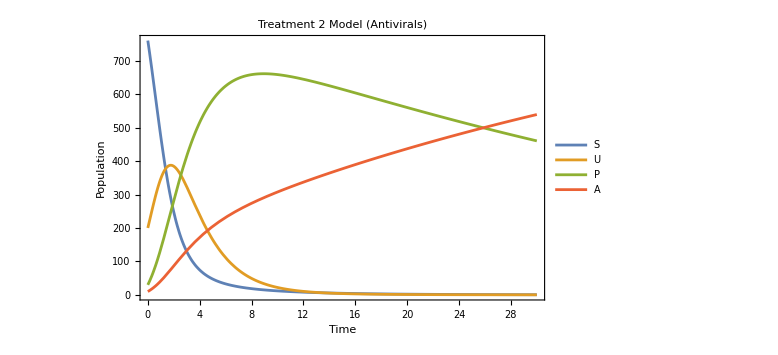

S[t]: {0.515372,760.}

U[t]: {0.197245,384.437}

P[t]: {30.,660.953}

A[t]: {10.,539.038}

```mathematica
params2={α->0.5,β->.15,ω->0.2/10,ϵ->.784,μ->(.2)/10,c->10,τ->0.04};
soltreat2=NDSolve[treat2/.params2,{S,U,P,A},{t,0,10000}];
Plot[Evaluate[{S[t],U[t],P[t],A[t]}/.soltreat2],{t,0,30},
		PlotLabel->"Treatment 2 Model (Antivirals)",PlotLegends->Placed[{"S","U","P","A"},Right],Frame->True,Axes->False,FrameLabel->{"Time","Population"},ImageSize->Large]

Print["S[t]: ",MinMax[Table[{S[t]}/. soltreat2,{t,0,30}]]]
Print["U[t]: ",MinMax[Table[{U[t]}/. soltreat2,{t,0,30}]]]
Print["P[t]: ",MinMax[Table[{P[t]}/. soltreat2,{t,0,30}]]]
Print["A[t]: ",MinMax[Table[{A[t]}/. soltreat2,{t,0,30}]]]
```

## Treatment 3 Model (Needle Exchange)

```mathematica
treat3={
S'[t]==-(β c S[t]U[t])/1000-(ω c S[t]P[t])/1000-τ S[t],
U'[t]==(β c S[t]U[t])/1000+(ω c S[t]P[t])/1000-α U[t]+τ S[t],
P'[t]==ϵ α U[t]-μ P[t] ,
A'[t]==(1-ϵ)α U[t]+μ P[t],
S[0]==760,U[0]==200,P[0]==30,A[0]==10
	};
```

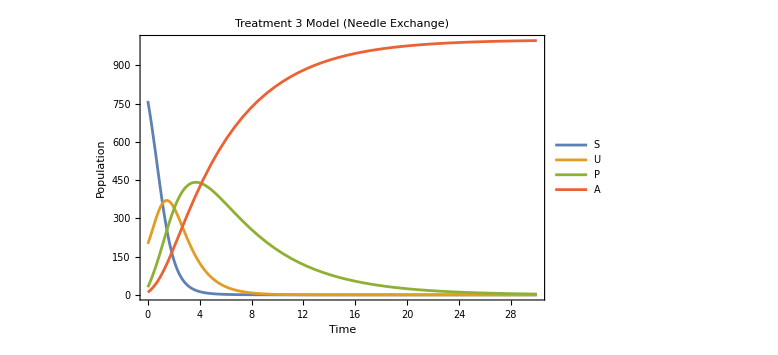

S[t]: {0.0252176,760.}

U[t]: {0.0010168,347.002}

P[t]: {3.26085,439.096}

A[t]: {10.,996.713}

```mathematica
params3={α->0.75,β->.15,ω->0.2,ϵ->.784,μ->.2,c->10,τ->0.04/2};
soltreat3=NDSolve[treat3/.params3,{S,U,P,A},{t,0,10000}];
Plot[Evaluate[{S[t],U[t],P[t],A[t]}/.soltreat3],{t,0,30},
		PlotLabel->"Treatment 3 Model (Needle Exchange)",PlotLegends->Placed[{"S","U","P","A"},Right],Frame->True,Axes->False,FrameLabel->{"Time","Population"},ImageSize->Large]

Print["S[t]: ",MinMax[Table[{S[t]}/. soltreat3,{t,0,30}]]]
Print["U[t]: ",MinMax[Table[{U[t]}/. soltreat3,{t,0,30}]]]
Print["P[t]: ",MinMax[Table[{P[t]}/. soltreat3,{t,0,30}]]]
Print["A[t]: ",MinMax[Table[{A[t]}/. soltreat3,{t,0,30}]]]
```

## General Model Definition & Parameter Table

```mathematica
ClearAll["Global`*"];
vars={s,u,p,a};
reducedVars={s,u,p};
rhs={
-beta*c*s*u/1000-omega*c*s*p/1000-tau*s,
beta*c*s*u/1000+omega*c*s*p/1000-alpha*u+tau*s,
epsilon*alpha*u-mu*p,
(1-epsilon)*alpha*u+mu*p
};
initialState={760,200,30,10};
scenarioNames={"Base","Treatment 1","Treatment 2","Treatment 3"};
parameterSets=Association[
"Base"->{alpha->0.5,beta->0.15,omega->0.2,epsilon->0.784,mu->0.2,c->10,tau->0},
"Treatment 1"->{alpha->0.75,beta->0.15/2,omega->0,epsilon->0.784,mu->0.2,c->5,tau->0.4},
"Treatment 2"->{alpha->0.75,beta->0.15,omega->0.2/10,epsilon->0.784,mu->0.2/10,c->10,tau->0.4},
"Treatment 3"->{alpha->0.75,beta->0.15,omega->0,epsilon->0.784,mu->0.2,c->10,tau->0.2}
];
parameterTable=Dataset[
Map[
Function[{name},
Association[
"Scenario"->name,
"alpha"->ReplaceAll[alpha,parameterSets[name]],
"beta"->ReplaceAll[beta,parameterSets[name]],
"omega"->ReplaceAll[omega,parameterSets[name]],
"epsilon"->ReplaceAll[epsilon,parameterSets[name]],
"mu"->ReplaceAll[mu,parameterSets[name]],
"c"->ReplaceAll[c,parameterSets[name]],
"tau"->ReplaceAll[tau,parameterSets[name]]
]
],
scenarioNames
]
];
parameterTable
```

## Find the equilibria

Equilibrium is a state where all of our derivatives are zero. Calculation requires the four dependent variables to be nonnegative and to sum to 1000.

```mathematica
Clear[equilibriumConditions,equilibriumResults,equilibriumDataset];

(*Define the equilibrium requirements*)
equilibriumConditions=Apply[And,Thread[rhs==0]]&&s+u+p+a==1000&&Apply[And,Thread[vars>=0]];

(*Calculate the complete feasible equilibrium set for each model*)
equilibriumResults=AssociationMap[Function[{name},FullSimplify[Reduce[ReplaceAll[equilibriumConditions,parameterSets[name]],{s,u,p,a},Reals]]],scenarioNames];

(*Construct and validate the equilibrium Dataset*)
equilibriumDataset=Dataset[Map[Function[{name},Module[{parameters,result,zeroDerivativeCondition,populationCondition,nonnegativeCondition,terminalPointCondition,derivativeCheck,populationCheck,nonnegativeCheck,isSingleTerminalPoint,equilibriumType},parameters=parameterSets[name];
result=equilibriumResults[name];
(*Conditions used to validate the result*)zeroDerivativeCondition=Apply[And,Thread[ReplaceAll[rhs,parameters]==0]];
populationCondition=s+u+p+a==1000;
nonnegativeCondition=Apply[And,Thread[{s,u,p,a}>=0]];
terminalPointCondition=Apply[And,Thread[{s,u,p,a}=={0,0,0,1000}]];
(*Verify that every equilibrium makes all four derivatives equal zero*)derivativeCheck=TrueQ[Resolve[ForAll[{s,u,p,a},Implies[result,zeroDerivativeCondition]],Reals]];
(*Verify that every equilibrium has total population 1000*)populationCheck=TrueQ[Resolve[ForAll[{s,u,p,a},Implies[result,populationCondition]],Reals]];
(*Verify that every equilibrium is nonnegative*)nonnegativeCheck=TrueQ[Resolve[ForAll[{s,u,p,a},Implies[result,nonnegativeCondition]],Reals]];
(*Determine whether the equilibrium set is exactly the single point (0,0,0,1000)*)isSingleTerminalPoint=TrueQ[Resolve[ForAll[{s,u,p,a},Equivalent[result,terminalPointCondition]],Reals]];
equilibriumType=If[isSingleTerminalPoint,"Single equilibrium","Family of equilibria"];
Association["Model"->name,"Equilibrium calculated"->result,"Equilibrium type"->equilibriumType,"All derivatives equal zero"->derivativeCheck,"Population equals 1000"->populationCheck,"All compartments are nonnegative"->nonnegativeCheck]]],scenarioNames]];

equilibriumDataset
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

Resolve::ratnz: Resolve was unable to eliminate quantifiers from the system with inexact coefficients. The answer was obtained by eliminating quantifiers from a corresponding exact system and numericizing the result.

General::stop: Further output of Resolve::ratnz will be suppressed during this calculation.

## Classify stability

The Jacobian measures how small changes behave near an equilibrium. Negative eigenvalues mean the model returns toward the equilibrium. A positive eigenvalue means small changes can grow.

```mathematica
Clear[fullJacobian,baseFullJacobian,baseInfectedBlock,baseTrace,baseDeterminant,baseDiscriminant,baseLambdaMinus,baseLambdaPlus,baseFullEigenvalues,baseThreshold,baseClassification,treatmentFullEigenvalues,treatmentRelevantEigenvalues,treatmentStabilitySummary,lambda];

(*Calculate the full 4 x 4 Jacobian*)
fullJacobian=Table[D[Part[rhs,i],Part[vars,j]],{i,1,4},{j,1,4}];

(*Base equilibrium family:(S*,0,0,1000-S*)
baseFullJacobian=FullSimplify[ReplaceAll[ReplaceAll[fullJacobian,{s->sStar,u->0,p->0,a->1000-sStar}],parameterSets["Base"]]];

(*The two nonzero eigenvalues come from the U-P portion of the Jacobian*)
baseInfectedBlock=Part[baseFullJacobian,{2,3},{2,3}];

baseTrace=Factor[Tr[baseInfectedBlock]];

baseDeterminant=Factor[Det[baseInfectedBlock]];

baseDiscriminant=Factor[baseTrace^2-4*baseDeterminant];

(*Explicit formulas for the two S*-dependent eigenvalues*)
baseLambdaMinus=FullSimplify[(baseTrace-Sqrt[baseDiscriminant])/2,Assumptions->0<=sStar<=1000];

baseLambdaPlus=FullSimplify[(baseTrace+Sqrt[baseDiscriminant])/2,Assumptions->0<=sStar<=1000];

(*The full base-model eigenvalue list has two zero eigenvalues*)
baseFullEigenvalues={0,0,baseLambdaMinus,baseLambdaPlus};

(*Mathematica calculates the cutoff by finding where the determinant becomes zero*)
baseThreshold=First[ReplaceAll[sStar,Solve[baseDeterminant==0,sStar,Reals]]];

(*Verify that the displayed eigenvalues reproduce the characteristic polynomial*)
baseEigenvalueVerification=FullSimplify[CharacteristicPolynomial[baseFullJacobian,lambda]==Expand[lambda^2*(lambda-baseLambdaMinus)*(lambda-baseLambdaPlus)],Assumptions->0<=sStar<=1000];

(*Mathematically verify the signs of the two S*-dependent eigenvalues*)
belowThresholdCheck=FullSimplify[baseLambdaMinus<0&&baseLambdaPlus<0,Assumptions->0<=sStar<baseThreshold];

atThresholdCheck=FullSimplify[baseLambdaMinus<0&&baseLambdaPlus==0,Assumptions->sStar==baseThreshold];

aboveThresholdCheck=FullSimplify[baseLambdaMinus<0&&baseLambdaPlus>0,Assumptions->baseThreshold<sStar<=1000];

baseClassification=Dataset[{Association["Range of S*"->0<=sStar<baseThreshold,"Sign of lambda-minus"->"Negative","Sign of lambda-plus"->"Negative","Mathematically verified"->belowThresholdCheck,"Classification"->"Stable against small U and P disturbances"],Association["Range of S*"->sStar==baseThreshold,"Sign of lambda-minus"->"Negative","Sign of lambda-plus"->"Zero","Mathematically verified"->atThresholdCheck,"Classification"->"Threshold case"],Association["Range of S*"->baseThreshold<sStar<=1000,"Sign of lambda-minus"->"Negative","Sign of lambda-plus"->"Positive","Mathematically verified"->aboveThresholdCheck,"Classification"->"Unstable"]}];

(*Calculate all four eigenvalues for each treatment*)
treatmentNames=Rest[scenarioNames];

treatmentFullEigenvalues=AssociationMap[Function[{name},Sort[FullSimplify[Eigenvalues[ReplaceAll[ReplaceAll[fullJacobian,{s->0,u->0,p->0,a->1000}],parameterSets[name]]]]]],treatmentNames];

(*Remove the structural zero eigenvalue when classifying stability on the fixed population surface*)
treatmentRelevantEigenvalues=AssociationMap[Function[{name},DeleteCases[treatmentFullEigenvalues[name],0]],treatmentNames];

treatmentStabilitySummary=Dataset[Map[Function[{name},Module[{fullValues,relevantValues,allNegative},fullValues=treatmentFullEigenvalues[name];
relevantValues=treatmentRelevantEigenvalues[name];
allNegative=TrueQ[Apply[And,Thread[relevantValues<0]]];
Association["Model"->name,"Full 4 x 4 eigenvalues"->fullValues,"Relevant eigenvalues when population is fixed"->relevantValues,"All relevant eigenvalues negative"->allNegative,"Classification"->If[allNegative,"Stable","Unstable"]]]],treatmentNames]];

(*Display the complete analysis*)
Column[{Style["Full 4 x 4 Jacobian",15,Bold],MatrixForm[fullJacobian],Style["Base-model Jacobian at (S*,0,0,1000-S*)",15,Bold],MatrixForm[baseFullJacobian],Style["Two eigenvalues that depend on S*",15,Bold],Grid[{{"Eigenvalue","Formula"},{"lambda-minus",baseLambdaMinus},{"lambda-plus",baseLambdaPlus}},Frame->All,Alignment->Left],Style["Complete base-model eigenvalue list",15,Bold],baseFullEigenvalues,Grid[{{"Quantity","Result"},{"Trace of U-P block",baseTrace},{"Determinant of U-P block",baseDeterminant},{"Cutoff value",baseThreshold},{"Numerical cutoff",N[baseThreshold,8]},{"Eigenvalue formula verified",baseEigenvalueVerification}},Frame->All,Alignment->Left],Style["Base-model stability classification",15,Bold],baseClassification,Style["Treatment stability classification",15,Bold],treatmentStabilitySummary},Spacings->2]
```

Full 4 x 4 Jacobian
(-(c omega p)/1000-tau-(beta c u)/1000 | -(beta c s)/1000 | -(c omega s)/1000 | 0
(c omega p)/1000+tau+(beta c u)/1000 | -alpha+(beta c s)/1000 | (c omega s)/1000 | 0
0 | alpha epsilon | -mu | 0
0 | alpha (1-epsilon) | mu | 0)
Base-model Jacobian at (S*,0,0,1000-S*)
(0 | -0.0015 sStar | -0.002 sStar | 0
0 | -0.5+0.0015 sStar | 0.002 sStar | 0
0 | 0.392 | -0.2 | 0
0 | 0.108 | 0.2 | 0)
Two eigenvalues that depend on S*
Eigenvalue | Formula
lambda-minus | -0.35+0.00075 sStar-0.00075 √(40000.+sStar (993.778+1. sStar))
lambda-plus | -0.35+0.00075 sStar+0.00075 √(40000.+sStar (993.778+1. sStar))
Complete base-model eigenvalue list
{0,0,-0.35+0.00075 sStar-0.00075 √(40000.+sStar (993.778+1. sStar)),-0.35+0.00075 sStar+0.00075 √(40000.+sStar (993.778+1. sStar))}
Quantity | Result
Trace of U-P block | 0.0015 (-466.667+1. sStar)
Determinant of U-P block | -0.001084 (-92.2509+1. sStar)
Cutoff value | 92.2509
Numerical cutoff | 92.2509
Eigenvalue formula verified | True
Base-model stability classification

Treatment stability classification

## Numerical Validation & Long Term Trajectory plots

The plotting horizons emphasize the transient behavior of each scenario. The integrations themselves extend to the longer horizons used in the numerical-check table.

```mathematica
Clear[solveScenario,solutions,terminalStates,maxConservationErrors,numericalCheckTable,trajectoryPlots];

scenarioNames={"Base","Treatment 1","Treatment 2","Treatment 3"};

(*Protect against machine-precision parameters from the original notebook*)
exactRhs=Rationalize[rhs,10^-12];
exactInitialState=Rationalize[initialState,10^-12];

(*Solve one named scenario*)
solveScenario=Function[{name,tmax},Module[{ss,uu,pp,aa,rules,equations},rules=Rationalize[parameterSets[name],10^-12];
equations=Thread[{Derivative[1][ss][t],Derivative[1][uu][t],Derivative[1][pp][t],Derivative[1][aa][t]}==ReplaceAll[ReplaceAll[exactRhs,Thread[vars->{ss[t],uu[t],pp[t],aa[t]}]],rules]];
NDSolveValue[Join[equations,Thread[{ss[0],uu[0],pp[0],aa[0]}==exactInitialState]],{ss,uu,pp,aa},{t,0,tmax},WorkingPrecision->30,AccuracyGoal->18,PrecisionGoal->18,MaxSteps->Infinity]]];

(*Long integration horizons used for numerical validation*)
timeHorizons=Association["Base"->1000,"Treatment 1"->1000,"Treatment 2"->1000,"Treatment 3"->1000];

(*Solve all four models*)
solutions=AssociationMap[Function[{name},solveScenario[name,timeHorizons[name]]],scenarioNames];

(*State at the end of each integration*)
terminalStates=AssociationMap[Function[{name},Chop[N[Through[(solutions[name])[timeHorizons[name]]],12],10^-8]],scenarioNames];

(*Check population conservation at 201 sampled times*)
maxConservationErrors=AssociationMap[Function[{name},Max[Abs[Table[Total[Through[(solutions[name])[tt]]]-1000,{tt,0,timeHorizons[name],timeHorizons[name]/200}]]]],scenarioNames];

(*Assemble numerical-validation table*)
numericalCheckTable=Dataset[Map[Function[{name},Association["Scenario"->name,"Final time"->timeHorizons[name],"State at final time"->terminalStates[name],"Maximum sampled population error"->N[maxConservationErrors[name],6]]],scenarioNames]];

plotHorizons=Association["Base"->100,"Treatment 1"->100,"Treatment 2"->100,"Treatment 3"->100];

trajectoryPlots=AssociationMap[Function[{name},With[{sol=solutions[name],tEnd=plotHorizons[name]},Plot[Evaluate[Table[sol[[i]][t],{i,1,4}]],{t,0,tEnd},(*Prevent artificial gaps in continuous solutions*)Exclusions->None,PlotPoints->150,MaxRecursion->6,PerformanceGoal->"Quality",PlotStyle->{Directive[Blue,AbsoluteThickness[2.2]],Directive[Orange,AbsoluteThickness[2.2]],Directive[Darker[Green],AbsoluteThickness[2.2]],Directive[Red,AbsoluteThickness[2.2]]},PlotLegends->Placed[{"S","U","P","A"},Below],PlotLabel->Style[name,14,Bold],PlotRange->{{0,tEnd},{0,1000}},Frame->True,Axes->False,FrameLabel->{"Time","Population"},ImageSize->500]]],scenarioNames];

Column[{Style["Numerical validation",16,Bold],numericalCheckTable,Style["Trajectories for all four scenarios",16,Bold],GraphicsGrid[Partition[Lookup[trajectoryPlots,scenarioNames],2],Spacings->{0.4,0.7},ImageSize->1100]},Spacings->2]
```

Numerical validation

Trajectories for all four scenarios
-Graphics-